## EP-2 Line and EP-3 point in 2D parameter space

```mathematica
Clear["Global`*"]
```

```mathematica
C0=1;
R0=3/5;
ham[δ_,R0_,G_]:={{δ+I G,R0,C0},{R0,0,R0},{C0,R0,δ-I G}};
ham[δ,R0,G]//MatrixForm
```

(ⅈ G+δ | 3/5 | 1
3/5 | 0 | 3/5
1 | 3/5 | -ⅈ G+δ)

```mathematica
compcond=Simplify[Discriminant[Det[ham[δ,R0,G]-IdentityMatrix[3]e],e]]
```

-4 G^6+G^4 (516/25-8 δ^2)+(4 (16-25 δ)^2 (97+50 δ+25 δ^2))/15625+G^2 (-22188/625+(648 δ)/25+(8 δ^2)/5-4 δ^4)

```mathematica
Collect[-Det[ham[δ,R0,G]-IdentityMatrix[3]e],e];

a2=-Coefficient[Collect[-Det[ham[δ,R0,G]-IdentityMatrix[3]e],e],e,2];
a3=-Coefficient[Collect[-Det[ham[δ,R0,G]-IdentityMatrix[3]e],e],e,3];
a1=Coefficient[Collect[-Det[ham[δ,R0,G]-IdentityMatrix[3]e],e],e,1];
a0=-Coefficient[Collect[-Det[ham[δ,R0,G]-IdentityMatrix[3]e],e],e,0];
```

```mathematica
realcond=(a1-3a0/a2)/2-(a2/3)^2;
```

```mathematica
engeq=With[{δ0=1/2},(Det[ham[δ,R0,G]-IdentityMatrix[3]e]/.Solve[Evaluate[realcond/.{δ->δ0}]==0,G∈Reals][[2]])/.{δ->δ0}]
Solve[engeq==0,e]//N
```

9/25-(293 e)/225+e^2-e^3

{{e→0.333333},{e→0.333333-0.984322 ⅈ},{e→0.333333+0.984322 ⅈ}}

```mathematica
Gc=(DeleteDuplicates[G/.Solve[{Numerator[Resultant[realcond,compcond,δ]]==0,G∈Reals,G>0},G]][[1]])
δc=(δ/.Solve[{Evaluate[realcond/.{G->Gc}]==0,δ∈Reals,δ>0},δ])[[1]]
e/.Solve[Det[ham[δc,R0,Gc]-e IdentityMatrix[3]]==0,e]//N
```

Root1.39Root[-410758+989625 #1^2-885000 #1^4+250000 #1^6&,2]1.3892973136473576

Root0.794Root[{-410758+989625 #1^2-885000 #1^4+250000 #1^6&,-243-144 #2+225 #1^2 #2+25 #2^3&},{2,1}]0.7940031971744785

{0.529335,0.529335,0.529335}

```mathematica
Show[ContourPlot[compcond==0,{δ,0,2},{G,0,3},PlotPoints->100,ContourStyle->Directive[Black,Thickness[0.005]]],ContourPlot[realcond==0,{δ,0,δc},{G,0,3},PlotPoints->100,ContourStyle->Directive[Black,Dashed,Thickness[0.005]]],Graphics[{Red,PointSize[0.02],Opacity[0.7],Point[N@{δc,Gc}]}],Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{"δ","G"}]
```

ContourPlot::plln: Limiting value δc in {δ,0,δc} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,ContourPlot[realcond==0,{δ,0,δc},{G,0,3},PlotPoints→100,ContourStyle→Directive[Black,Dashed,Thickness[0.005]]],,Frame→True,FrameStyle→Directive[color,16],FrameLabel→{δ,G}].

Show[-Graphics-,ContourPlot[realcond==0,{δ,0,δc},{G,0,3},PlotPoints→100,ContourStyle→Directive[Black,Dashed,Thickness[0.005]]],-Graphics-,Frame→True,FrameStyle→Directive[GrayLevel[0],16],FrameLabel→{δ,G}]

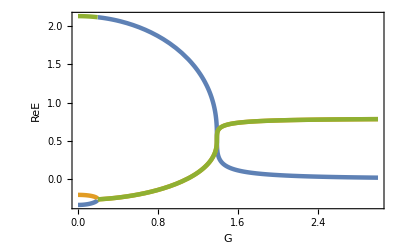

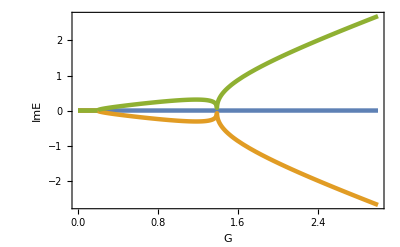

```mathematica
F1=With[{δ=δc,R0=R0},Plot[{Evaluate[Re[Eigenvalues[ham[δ,R0,G]]]]},{G,0,3},PlotStyle->{Thickness[0.008]},PlotRange->All,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{"G","ReE"}]]
F2=With[{δ=δc,R0=R0},Plot[{Evaluate[Im[Eigenvalues[ham[δ,R0,G]]]]},{G,0,3},PlotStyle->{Thickness[0.008]},PlotRange->All,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{"G","ImE"}]]
```

The eigenspace at EP-3 collapse into one dimension.

```mathematica
N[Eigensystem@ham[δc,R0,Gc]]//MatrixForm
Solve[Discriminant[Det[ham[δ,R0,0]-e IdentityMatrix[3]],e]==0,δ∈Reals]//N
```

(0.529335 | 0.529335 | 0.529335
{-0.562328+0.826914 ⅈ,0.4961+0.937305 ⅈ,1.} | {0.,0.,0.} | {0.,0.,0.})

{{δ→0.64},{δ→0.64}}

## Full phase diagram in three-level system

```mathematica
Clear["Global`*"]
```

```mathematica
C0=1;
ham[δ_,R0_,G_]:={{δ+I G,R0,C0},{R0,0,R0},{C0,R0,δ-I G}};
ham[δ,R0,G]//MatrixForm
```

(ⅈ G+δ | R0 | 1
R0 | 0 | R0
1 | R0 | -ⅈ G+δ)

```mathematica
EP2Surf[δ_,R0_,G_]:=Simplify[Discriminant[Det[ham[δ,R0,G]-IdentityMatrix[3]e],e]]
EP2Surf[δ,R0,G]
```

-4 (G^6+G^4 (-3-6 R0^2+2 δ^2)-(-1+R0^2+δ)^2 (8 R0^2+(1+δ)^2)+G^2 (3+12 R0^4-4 δ^2+δ^4+2 R0^2 (6-9 δ+5 δ^2)))

```mathematica
P1=Show[ContourPlot3D[Evaluate[EP2Surf[δ,R0,G]]==0,{δ,-2,1.5},{R0,0,1.5},{G,0,3},PlotPoints->80,ContourStyle->{RGBColor[0,.4,1,.6]},Mesh->None,PlotRange->All],Frame->True,AxesLabel->{"δ","R0","G"},Boxed->True,AxesStyle->Directive[Black,14],ImageSize->300]
```

-Graphics3D-

```mathematica
Collect[-Det[ham[δ,R0,G]-IdentityMatrix[3]e],e]
a2=-Coefficient[Collect[-Det[ham[δ,R0,G]-IdentityMatrix[3]e],e],e,2];
a1=Coefficient[Collect[-Det[ham[δ,R0,G]-IdentityMatrix[3]e],e],e,1];
a0=-Coefficient[Collect[-Det[ham[δ,R0,G]-IdentityMatrix[3]e],e],e,0];
```

e^3-2 R0^2-2 e^2 δ+2 R0^2 δ+e (-1+G^2-2 R0^2+δ^2)

```mathematica
ReEquSurf=Numerator@Simplify[(a1-3a0/a2)/2-(a2/3)^2]
```

9 R0^2 (-3+δ)+δ (-9+9 G^2+δ^2)

```mathematica
RealSurf=Show[ContourPlot3D[ReEquSurf==0,{δ,-2,1.5},{R0,0,1.5},{G,0,3},PlotPoints->80,ContourStyle->{RGBColor[1,.4,0,.6]},Mesh->None,PlotRange->All],Frame->True,AxesLabel->{"δ","R0","G"}];
Show[P1,RealSurf,PlotRange->All];
```

```mathematica
EP3EqG=FactorList[Simplify[Resultant[EP2Surf[δ,R0,G],ReEquSurf,G]]];
MatrixForm[EP3EqG]
EP3ProjLineG=EP3EqG[[2,1]];
EP3G0=FactorList[EP2Surf[δ,R0,0]];
EP3G0//MatrixForm
```

(16 | 1
-27 R0^2+27 R0^2 δ+4 δ^3 | 6)

(4 | 1
-1+R0^2+δ | 2
1+8 R0^2+2 δ+δ^2 | 1)

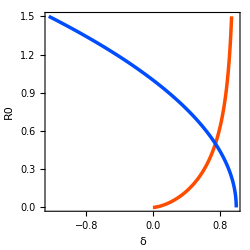

```mathematica
Show[ContourPlot[{EP3ProjLineG==0,EP3G0[[2,1]]==0},{δ,-2,1.5},{R0,0,1.5},PlotPoints->50,ContourStyle->{{RGBColor[1,.3,0,1],Thickness[0.01]},{RGBColor[0,.3,1,1],Thickness[0.01]}},PlotRange->All],Frame->True,FrameLabel->{"δ","R0"},FrameStyle->Directive[Black,16],PlotRange->All,ImageSize->250]
```

```mathematica
EP3Line=ImplicitRegion[ReEquSurf==0&&EP2Surf[δ,R0,G]==0,{δ,R0,G}];
L1=DiscretizeRegion[EP3Line,{{-3,1.5},{0,1.5},{0,3}},Method->{"DualMarchingCubes",PlotPoints->200},MeshCellStyle->{RGBColor[.3,1,0,.5]}];
```

```mathematica
P2=ContourPlot3D[ReEquSurf==0,{δ,-2,1.5},{R0,0,1.5},{G,0,3},RegionFunction->Function[{x,y,z},Evaluate[EP2Surf[x,y,z]<0]],RegionBoundaryStyle->None,ContourStyle->{RGBColor[1,.4,0,.6]},BoundaryStyle->None,Mesh->None,PerformanceGoal->"Quality",PlotPoints->80];
```

```mathematica
Evaluate[EP2Surf[δ,R0,0]]
DPLine=ImplicitRegion[δ==1-R0^2&&G==0,{δ,R0,G}];
L2=DiscretizeRegion[DPLine,{{-2,1.5},{0,1.5},{0,3}},Method->{"DualMarchingCubes",PlotPoints->200},MeshCellStyle->{Darker@Blue,Opacity[0.5]}];
```

4 (-1+R0^2+δ)^2 (8 R0^2+(1+δ)^2)

```mathematica
Show[P1,P2,L1,L2,Boxed->True,AxesStyle->Directive[Black,14],ImageSize->300]
```

-Graphics3D-

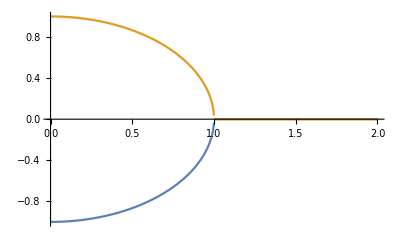

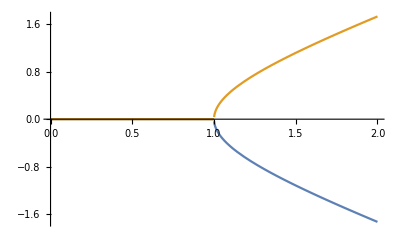

```mathematica
κ=1;
Plot[Evaluate[ComplexExpand@Re[Eigenvalues[{{-I γ,κ},{κ,I γ}}]]],{γ,0,2}]
Plot[Evaluate[ComplexExpand@Im[Eigenvalues[{{-I γ,κ},{κ,I γ}}]]],{γ,0,2}]
```